## Reproducing the purification sequence with gates derived from the hamiltonian

This notebook explores the purification sequence by simulating the hamiltonian (in secular approximation).
We aim to synthesize the following gate sequence. With the assumption that we generate a perfect state on the electron spins (i.e. V=1)
-Graphics-

```mathematica
basedirLT4 = "/Users/humphreys/Repositories/personal_calcs/Work/Modelling/PulseSim/LT4/";
basedirLT3 = "/Users/humphreys/Repositories/personal_calcs/Work/Modelling/PulseSim/LT3/";
```

```mathematica
Quiet[Needs["QDENSITY`Qdensity`"]];
```

Type "?intro", "?QDENSITY`Qdensity`*" or "?about for help.

## Basic setup

General useful definitions such as gates etc.

```mathematica
KP[r__]:=KroneckerProduct[r]
StyleNumber[number_] :=Style[number,Bold,Darker[Green]]
Stokesfromρ[ρ_]:=(t =Table[Re[Tr[Subscript[σ, i].ρ]],{i,1,3}]//N; t)
StokesfromρStyled[ρ_]:=(t =Table[If[Abs[Re[Tr[Subscript[σ, i].ρ]]]>0.4,StyleNumber[Re[Tr[Subscript[σ, i].ρ]]],Re[Tr[Subscript[σ, i].ρ]]],{i,1,3}]//N; t)
ρfromψ[ψ_] :=ψ.ψ†;
Stokesfromψ[ψ_]:=Stokesfromρ[ρfromψ[ψ]];
Fidfromρ[ρ_,σ_]:=Re[Tr[MatrixPower[MatrixPower[ρ,0.5].σ.MatrixPower[ρ,0.5],0.5]]^2];
MixedState=𝕀/2;(*Mixed state*)
transformAndNorm[state_,U_]:=(out=U.state.U†;out=out/Tr[out]);
norm[state_]:=state/Tr[state];
transform[state_,U_]:=U.state.U†;

measureOut[state_]:=KP[Subscript[𝒫, 0],Subscript[σ, 0]].state.KP[Subscript[𝒫, 0],Subscript[σ, 0]]†+KP[Subscript[𝒫, 1],Subscript[σ, 0]].state.KP[Subscript[𝒫, 1],Subscript[σ, 0]]†;
measureOutAndBranch[state_,U0_,U1_]:=U0.KP[Subscript[𝒫, 0],Subscript[σ, 0]].state.KP[Subscript[𝒫, 0],Subscript[σ, 0]]†.U0†+U1.KP[Subscript[𝒫, 1],Subscript[σ, 0]].state.KP[Subscript[𝒫, 1],Subscript[σ, 0]]†.U1†;
```

```mathematica
(*Single qubit gates*)
{rxp,rXp,ryp,rYp,rzp,rZp}=Table[AF[MatrixExp[-ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
{rxm,rXm,rym,rYm,rzm,rZm}=Table[AF[MatrixExp[ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
rThetaX[θ_]=MatrixExp[-ⅈ*Subscript[σ, 1]*θ/2];
rThetaY[θ_]=MatrixExp[-ⅈ*Subscript[σ, 2]*θ/2];
rThetaZ[θ_]=MatrixExp[-ⅈ*Subscript[σ, 3]*θ/2];
rThetaϕ[θ_,ϕ_]=MatrixExp[-ⅈ*(Cos[ϕ] Subscript[σ, 1]*θ+Sin[ϕ] Subscript[σ, 2]*θ)/2];
```

```mathematica
(*This function brute forces the problem by looping over all expectation values
This probably not the most efficient method but good enough for 16x16 matrices*)
Raffleρ4Q[ρ_]:=(
ρNew = ConstantArray[0,{16,16}] ;(*Init matrix*)
Do[ρNew+=0.5^4*Tr[KP[Subscript[σ, i],Subscript[σ, j],Subscript[σ, k],Subscript[σ, l]].ρ]*KP[Subscript[σ, i],Subscript[σ, k],Subscript[σ, j],Subscript[σ, l]],{i,0,3},{j,0,3},{k,0,3},{l,0,3}];
ρNew
)
```

Our nuclear spin parameters for both setups:

```mathematica
(*LT3*)
ωL3 = 2*π*447747.11;
wL31=2*π*425341.4;
Aperp3 =2*π*(87.5)*10^3;
Apar3 = -2*π*(30.0)*10^3 ;
par3 = ωL3+Apar3;

(*LT4*)
ωL4 = 2π 443172.12;
ωL41=2π 416572.34;
Aperp4 =2*π*(35.0)*10^3;
Apar4 =-2*π*(33.0)*10^3 ; (*because we use the -1 transition here*)
par4=Apar4+ωL4;

(*carbon parameters as a list*)
LT3C = {ωL3,par3-545.2,1};
LT3C[[3]]=Sqrt[(wL31 )^2-LT3C[[2]]^2]; (*Gate parameters have to be slightly adjusted*)

LT4C={ωL4,par4+34349.1,1};
LT4C[[3]]=Sqrt[(ωL41)^2-LT4C[[2]]^2]; (*Gate parameters have to be slightly adjusted*)
```

The system Hamiltonian with NV and Carbon reads

```mathematica
Usys[t_,{ω_,par_,Aperp_}] := MatrixExp[-ⅈ t/2(ω KP[Subscript[𝒫, 0],Subscript[σ, 3]]+KP[Subscript[𝒫, 1],(par Subscript[σ, 3]+Aperp*Subscript[σ, 1])])];
```

Import the pulse sequences

```mathematica
getPulses[basedir_,measname_]:=Module[{filename,x,attrs,seqOverview,PulseSeqs},
filename=If[FileExtension["filename"]=="",measname<>".h5",measname];
seqOverview={};
attrs={"seq_overview/name","seq_overview/trigger_wait","seq_overview/goto_target","seq_overview/jump_target","seq_overview/final_time"};
For[x=1,x≤Dimensions[attrs][[1]],x++,AppendTo[seqOverview,Import[basedir<>filename,{"Datasets",attrs[[x]]}]]];
seqOverview=Transpose[seqOverview];
PulseSeqs={};
For[x=0,x<Dimensions[seqOverview][[1]],x++,AppendTo[PulseSeqs,Import[basedir<>filename,{"Datasets","pulses/"<>ToString[x]}]]];
seqOverview=Transpose[seqOverview];
Transpose[{Transpose[seqOverview],PulseSeqs}]]
```

Compiler!

Each pulse has a few params:
1.) Centre of pulse
2.) Pulse duration (less useful here)
3.) Phase angle of pulse - for some reason, in the compiled sequences, 0 encodes Y gate, π/2 encodes X gate, 3 π/2 encodes - X gate, π encodes - Y gate
4.) The rotation angle (basically pi/2 or pi)
5.) Special. 1 is repump, 2 is readout (readout is not implemented in all of the datasets, but is also not necessary)

The pulse seq also has some extra data, like what it jumps to, and most importantly, the total length of the pulse sequence.

```mathematica
compiledPulse[{ω_,Apar_,Aperp_},pulseData_,ignoreFinal_:False,triggerReadout_:False,readoutVal_:0]:=Module[{i,numPulses,evMat,pulseMat,pulseDelay,compiledPulse},
numPulses=Dimensions[pulseData[[2]]][[1]];
compiledPulse=IdentityMatrix[4];
For[i=1,i<=numPulses,i++,
pulseDelay=If[i==1, pulseData[[2,i,1]],(pulseData[[2,i,1]]-pulseData[[2,i-1,1]])];
evMat=Usys[pulseDelay,{ω,Apar,Aperp}];
pulseMat=Which[pulseData[[2,i,5]]==0,KP[rThetaϕ[pulseData[[2,i,4]],(π/2-pulseData[[2,i,3]])],Subscript[σ, 0]],pulseData[[2,i,5]]==1,KP[Subscript[𝒫, 0],Subscript[σ, 0]],pulseData[[2,i,5]]==2,If[triggerReadout,KP[Subscript[𝒫, readoutVal],Subscript[σ, 0]],KP[Subscript[σ, 0],Subscript[σ, 0]]]];
compiledPulse=pulseMat.evMat.compiledPulse;
];
pulseDelay=If[Not[ignoreFinal],(pulseData[[1,5]]-pulseData[[2,-1,1]]),0];
compiledPulse=Usys[pulseDelay,{ω,Apar,Aperp}].compiledPulse;
Return[compiledPulse]
]
```

## Elec to carbon swap (Purification)

### LT4

#### Setup

```mathematica
LT4SwapX=getPulses[basedirLT4,"AWG_seqs_pur_Swap_el_to_C_X"];
```

```mathematica
LT4SwapY=getPulses[basedirLT4,"AWG_seqs_pur_Swap_el_to_C_Y"];
```

```mathematica
LT4SwapZ=getPulses[basedirLT4,"AWG_seqs_pur_Swap_el_to_C_Z"];
```

Check that the pulses match in the different files (apart from where deliberately different):

```mathematica
For[z=1,z<=Dimensions[LT4SwapX][[1]],z++,If[LT4SwapX[[z,2]]!=LT4SwapZ[[z,2]],Print[z]]]
For[z=1,z<=Dimensions[LT4SwapX][[1]],z++,If[LT4SwapX[[z,2]]!=LT4SwapY[[z,2]],Print[z]]]
For[z=1,z<=Dimensions[LT4SwapY][[1]],z++,If[LT4SwapY[[z,2]]!=LT4SwapZ[[z,2]],Print[z]]]
Print["Elem lengths?"]
For[z=1,z<=Dimensions[LT4SwapX][[1]],z++,If[LT4SwapX[[z,1,5]]!=LT4SwapZ[[z,1,5]],Print[z]]]
For[z=1,z<=Dimensions[LT4SwapX][[1]],z++,If[LT4SwapX[[z,1,5]]!=LT4SwapY[[z,1,5]],Print[z]]]
```

2

5

8

2

5

8

2

5

8

Elem lengths?

```mathematica
LT4SwapX[[2,2]]==LT4SwapX[[5,2]]
LT4SwapX[[2,2]]==LT4SwapX[[8,2]]
```

True

True

Ok, setup the different bits of the sequence!

```mathematica
LT4SwapX[[;;,1]]
```

(C_Init4_y_pt0_tau_0_N_0 | 1 | C_Init4_y_pt0_tau_0_N_0 | LDE10 | 0.000977248
LDE10 | 0 | C_Init4_y_pt0_tau_0_N_0 | Tomo_y_pi2_init0_tau_0_N_0 | 0.000985448
Tomo_y_pi2_init0_tau_0_N_0 | 0 | None | None | 0.000456568
C_Init4_y_pt1_tau_0_N_0 | 1 | C_Init4_y_pt1_tau_0_N_0 | LDE11 | 0.00143182
LDE11 | 0 | C_Init4_y_pt1_tau_0_N_0 | Tomo_y_pi2_init1_tau_0_N_0 | 0.000985448
Tomo_y_pi2_init1_tau_0_N_0 | 0 | None | None | 0.000456004
C_Init4_y_pt2_tau_0_N_0 | 1 | C_Init4_y_pt2_tau_0_N_0 | LDE12 | 0.00143125
LDE12 | 0 | C_Init4_y_pt2_tau_0_N_0 | phase_gate_Tomo4_Ren_a_211_2_tau_0_N_0 | 0.000985448
phase_gate_Tomo4_Ren_a_211_2_tau_0_N_0 | 0 | None | None | 0.000890228)

```mathematica
InitLT4Swap=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapZ[[1]]];

InitEAndSwapLT4SwapX=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapX[[2]]];
InitEAndSwapLT4SwapY=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapY[[2]]];
InitEAndSwapLT4SwapZ=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapZ[[2]]];

InitSwap={InitEAndSwapLT4SwapX,InitEAndSwapLT4SwapY,InitEAndSwapLT4SwapZ};

TomoLT4XSwapX=compiledPulse[LT4C,LT4SwapZ[[3]]];
TomoLT4XSwapY=compiledPulse[LT4C,LT4SwapZ[[6]]];
TomoLT4XSwapZ=compiledPulse[LT4C,LT4SwapZ[[9]]];

TomoSwap={TomoLT4XSwapX,TomoLT4XSwapY,TomoLT4XSwapZ};
```

#### Sequences

Init sets the carbon to Z

```mathematica
pulseLT4=InitLT4Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT4]]
```

(0.998532+0. ⅈ | -0.0295592-0.0199572 ⅈ
-0.0295592+0.0199572 ⅈ | 0.00146845+0. ⅈ)

Swap sets the carbon to Z

```mathematica
bases={"X","Y","Z"};
For[j=1,j≤3,j++,Print["Input: "<>bases[[j]]];
pulseLT4=InitSwap[[j]].InitLT4Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
Print[PTr[{1},transformAndNorm[initState,pulseLT4]]//TableForm]
]
```

Input: X

0.999316+0. ⅈ | -0.0109478-0.0237375 ⅈ
-0.0109478+0.0237375 ⅈ | 0.000683902+0. ⅈ

Input: Y

0.524601+0. ⅈ | 0.0210336+0.498951 ⅈ
0.0210336-0.498951 ⅈ | 0.475399+0. ⅈ

Input: Z

0.510746+0. ⅈ | 0.499457-0.020663 ⅈ
0.499457+0.020663 ⅈ | 0.489254+0. ⅈ

How does it look in different tomo bases?

```mathematica
bases={"X","Y","Z"};
For[j=1,j≤3,j++,Print["Input: "<>bases[[j]]];For[i=1,i≤3,i++,
pulseLT4=TomoSwap[[i]].InitSwap[[j]].InitLT4Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT4]];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].outState]]]]]]
```

Input: X

X -0.00241272

Y -0.070201

Z 0.992431

Input: Y

X 0.0125593

Y 0.997014

Z 0.101344

Input: Z

X -0.999508

Y 0.0136355

Z -0.0631276

### LT3

#### Setup

```mathematica
LT3SwapX=getPulses[basedirLT3,"AWG_seqs_Pippin_SIL3_Swap_el_to_C_X"];
```

```mathematica
LT3SwapY=getPulses[basedirLT3,"AWG_seqs_Pippin_SIL3_Swap_el_to_C_Y"];
```

```mathematica
LT3SwapZ=getPulses[basedirLT3,"AWG_seqs_Pippin_SIL3_Swap_el_to_C_Z"];
```

Check that the pulses match in the different files (apart from where deliberately different):

```mathematica
For[z=1,z<=Dimensions[LT3SwapX][[1]],z++,If[LT3SwapX[[z,2]]!=LT3SwapZ[[z,2]],Print[z]]]
For[z=1,z<=Dimensions[LT3SwapX][[1]],z++,If[LT3SwapX[[z,2]]!=LT3SwapY[[z,2]],Print[z]]]
For[z=1,z<=Dimensions[LT3SwapY][[1]],z++,If[LT3SwapY[[z,2]]!=LT3SwapZ[[z,2]],Print[z]]]
Print["Elem lengths?"]
For[z=1,z<=Dimensions[LT3SwapX][[1]],z++,If[LT3SwapX[[z,1,5]]!=LT3SwapZ[[z,1,5]],Print[z]]]
For[z=1,z<=Dimensions[LT3SwapX][[1]],z++,If[LT3SwapX[[z,1,5]]!=LT3SwapY[[z,1,5]],Print[z]]]
```

2

5

8

2

5

8

2

5

8

Elem lengths?

```mathematica
LT3SwapX[[2,2]]==LT3SwapX[[5,2]]
LT3SwapX[[2,2]]==LT3SwapX[[8,2]]
```

True

True

Ok, setup the different bits of the sequence!

```mathematica
LT3SwapX[[;;,1]]
```

(C_Init1_y_pt0_tau_0_N_0 | 1 | C_Init1_y_pt0_tau_0_N_0 | LDE10 | 0.000977224
LDE10 | 0 | C_Init1_y_pt0_tau_0_N_0 | Tomo_y_pi2_init0_tau_0_N_0 | 0.000985424
Tomo_y_pi2_init0_tau_0_N_0 | 0 | None | None | 0.000282108
C_Init1_y_pt1_tau_0_N_0 | 1 | C_Init1_y_pt1_tau_0_N_0 | LDE11 | 0.00125683
LDE11 | 0 | C_Init1_y_pt1_tau_0_N_0 | Tomo_y_pi2_init1_tau_0_N_0 | 0.000985424
Tomo_y_pi2_init1_tau_0_N_0 | 0 | None | None | 0.000281552
C_Init1_y_pt2_tau_0_N_0 | 1 | C_Init1_y_pt2_tau_0_N_0 | LDE12 | 0.00125628
LDE12 | 0 | C_Init1_y_pt2_tau_0_N_0 | phase_gate_Tomo1_Ren_a_211_2_tau_0_N_0 | 0.000985424
phase_gate_Tomo1_Ren_a_211_2_tau_0_N_0 | 0 | None | None | 0.00053986)

```mathematica
InitLT3Swap=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,LT3SwapZ[[1]]];

InitEAndSwapLT3SwapX=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,LT3SwapX[[2]]];
InitEAndSwapLT3SwapY=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,LT3SwapY[[2]]];
InitEAndSwapLT3SwapZ=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,LT3SwapZ[[2]]];

InitSwap={InitEAndSwapLT3SwapX,InitEAndSwapLT3SwapY,InitEAndSwapLT3SwapZ};

TomoLT3XSwapX=compiledPulse[LT3C,LT3SwapZ[[3]]];
TomoLT3XSwapY=compiledPulse[LT3C,LT3SwapZ[[6]]];
TomoLT3XSwapZ=compiledPulse[LT3C,LT3SwapZ[[9]]];

TomoSwap={TomoLT3XSwapX,TomoLT3XSwapY,TomoLT3XSwapZ};
```

#### Sequences

Init sets the carbon to Z

```mathematica
pulseLT3=InitLT3Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT3]]
```

(0.989963+0. ⅈ | 0.0992799+0.00600262 ⅈ
0.0992799-0.00600262 ⅈ | 0.0100369+0. ⅈ)

Swap sets the carbon to Z

```mathematica
bases={"X","Y","Z"};
For[j=1,j≤3,j++,Print["Input: "<>bases[[j]]];
pulseLT3=InitSwap[[j]].InitLT3Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
Print[PTr[{1},transformAndNorm[initState,pulseLT3]]//TableForm]
]
```

Input: X

0.994107+0. ⅈ | 0.0615236+0.0455266 ⅈ
0.0615236-0.0455266 ⅈ | 0.00589259+0. ⅈ

Input: Y

0.501792+0. ⅈ | 0.291771-0.406038 ⅈ
0.291771+0.406038 ⅈ | 0.498208+0. ⅈ

Input: Z

0.577226+0. ⅈ | -0.400588-0.289077 ⅈ
-0.400588+0.289077 ⅈ | 0.422774+0. ⅈ

How does it look in different tomo bases?

```mathematica
bases={"X","Y","Z"};
For[j=1,j≤3,j++,Print["Input: "<>bases[[j]]];For[i=1,i≤3,i++,
pulseLT3=TomoSwap[[i]].InitSwap[[j]].InitLT3Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT3]];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].outState]]]]]]
```

Input: X

X 0.000398753

Y -0.151049

Z 0.94645

Input: Y

X -0.00570197

Y 0.987603

Z -0.0715466

Input: Z

X -0.999909

Y -0.0330291

Z 0.315398

## Check classical correlations

### LT4

#### Setup

```mathematica
ClassCorLT4X=getPulses[basedirLT4,"AWG_seqs_classical_correlations_onC13_X"];
```

```mathematica
ClassCorLT4X[[1;;6,1]]
ClassCorLT4X[[83;;89,1]]
```

(C_Init4_y_pt0_tau_0_N_0 | 1 | C_Init4_y_pt0_tau_0_N_0 | LDE10 | 0.000977248
LDE10 | 0 | C_Init4_y_pt0_tau_0_N_0 | LDE20 | 0.000985448
LDE20 | 0 | None | LDE_rephasing_2_0 | 7.×10^-6
LDE_rephasing_2_0 | 0 | None | Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | 9.392×10^-6
Single_C13_Phase_correct0_0_DD_elt_tau_2298_N_2 | 0 | None | Single_Final_C13_correct_even0_DD_elt_tau_2298_N_2 | 9.192×10^-6
Single_C13_Phase_correct0_1_DD_elt_tau_2298_N_2 | 0 | None | Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | 9.192×10^-6)

(Single_Final_C13_correct_even0_DD_elt_tau_2298_N_2 | 0 | Purify_y_pi2_init0_tau_0_N_0 | None | 8.192×10^-6
Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | 0 | None | None | 0.000010192
Purify_y_pi2_init0_tau_0_N_0 | 0 | Tomo1_y_pi2_init0_tau_0_N_0 | Tomo0_y_pi2_init0_tau_0_N_0 | 0.0005358
Tomo0_y_pi2_init0_tau_0_N_0 | 0 | Rome_0 | None | 0.000454568
Tomo1_y_pi2_init0_tau_0_N_0 | 0 | None | None | 0.000454368
C_Init4_y_pt1_tau_0_N_0 | 1 | C_Init4_y_pt1_tau_0_N_0 | LDE11 | 0.00143162
LDE11 | 0 | C_Init4_y_pt1_tau_0_N_0 | LDE21 | 0.000985448)

```mathematica
ClassCorLT4Y=getPulses[basedirLT4,"AWG_seqs_classical_correlations_onC13_Y"];
ClassCorLT4Z=getPulses[basedirLT4,"AWG_seqs_classical_correlations_onC13_Z"];
```

Check that the pulses match:

```mathematica
For[z=1,z<=Dimensions[ClassCorLT4X][[1]],z++,If[ClassCorLT4X[[z,2]]!=ClassCorLT4Y[[z,2]],Print[z]]]
For[z=1,z<=Dimensions[ClassCorLT4X][[1]],z++,If[ClassCorLT4X[[z,2]]!=ClassCorLT4Z[[z,2]],Print[z]]]
```

2

89

176

2

89

176

```mathematica
ClassCorLT4X[[2,2]]==ClassCorLT4X[[89,2]]
ClassCorLT4X[[2,2]]==ClassCorLT4X[[176,2]]
```

True

True

```mathematica
InitLT4=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,ClassCorLT4Z[[1]]];
LDESwapLT4X=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,ClassCorLT4X[[2]]];
LDESwapLT4Y=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,ClassCorLT4Y[[2]]];
LDESwapLT4Z=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,ClassCorLT4Z[[2]]];
LDE2LT4=compiledPulse[LT4C,ClassCorLT4Z[[3]]];
rephasingLT4=compiledPulse[LT4C,ClassCorLT4Z[[4]]];
c13PhaseCorEvenLT4=compiledPulse[LT4C,ClassCorLT4Z[[5]]];
c13PhaseCorOddLT4=compiledPulse[LT4C,ClassCorLT4Z[[6]]];
c13FinalCorEvenLT4=compiledPulse[LT4C,ClassCorLT4Z[[83]]];
c13FinalCorOddLT4=compiledPulse[LT4C,ClassCorLT4Z[[84]]];
PurLT4=compiledPulse[LT4C,ClassCorLT4Z[[85]]];
TomoLT4X=compiledPulse[LT4C,ClassCorLT4Y[[86]]];
TomoLT4Y=compiledPulse[LT4C,ClassCorLT4Y[[173]]];
TomoLT4Z=compiledPulse[LT4C,ClassCorLT4Y[[260]]];
TomoLT4Xmin=compiledPulse[LT4C,ClassCorLT4Z[[87]]];
TomoLT4Ymin=compiledPulse[LT4C,ClassCorLT4Z[[174]]];
TomoLT4Zmin=compiledPulse[LT4C,ClassCorLT4Z[[261]]];

TotalPhaseCompGateLT4[n_]:=If[Mod[n,2]==0,c13FinalCorOddLT4.MatrixPower[c13PhaseCorOddLT4.c13PhaseCorEvenLT4,n/2],
c13FinalCorEvenLT4.c13PhaseCorEvenLT4.MatrixPower[c13PhaseCorOddLT4.c13PhaseCorEvenLT4,(n-1)/2]];

inits={LDESwapLT4X,LDESwapLT4Y,LDESwapLT4Z};
tomos={TomoLT4X,TomoLT4Y,TomoLT4Z};
tomosMin={TomoLT4Xmin,TomoLT4Ymin,TomoLT4Zmin};
bases={"X","Y","Z"};
```

#### Calibrate phase offset

For this, need to change phase of LDE2 to match what was used for calibration

15

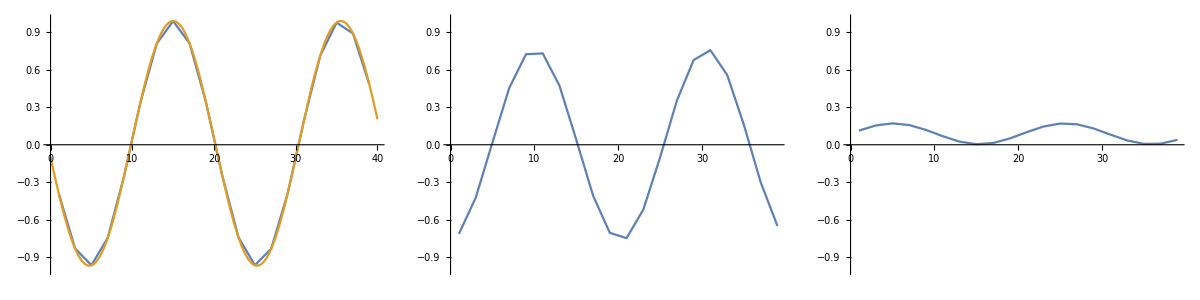

```mathematica
PhaseComp[n_]:=Module[{},pulseLT4=PurLT4.TotalPhaseCompGateLT4[n].rephasingLT4.KP[rzm,Subscript[σ, 0]].LDE2LT4.LDESwapLT4Y.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
outState=measureOutAndBranch[outState,TomoLT4Z,TomoLT4Zmin];
outState=norm[outState];
Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]
phaseCompSweep=Table[{n,PhaseComp[n]},{n,1,40,2}];
Clear[x,a];
nlmLT4=NonlinearModelFit[phaseCompSweep,Amp*Cos[2π f x-a]+off,{{f,1/20},{a,2π},{Amp,1},{off,0.5}},x];
xx=Show[ListPlot[phaseCompSweep,Joined->{True}],Plot[Normal[nlmLT4],{x,0,40},PlotStyle->{ColorData[97,"ColorList"][[2]]}],PlotRange->{Automatic,{-1,1}}];
offsetLT4=Round[If[Amp>0,Mod[a,2π],Mod[a+π,2π]]/(2π f)/.nlmLT4["BestFitParameters"]]

PhaseComp[n_]:=Module[{},pulseLT4=PurLT4.TotalPhaseCompGateLT4[n].rephasingLT4.KP[rzm,Subscript[σ, 0]].LDE2LT4.LDESwapLT4Y.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
outState=measureOutAndBranch[outState,TomoLT4X,TomoLT4Xmin];
outState=norm[outState];
Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]
phaseCompSweep=Table[{n,PhaseComp[n]},{n,1,40,2}];
yy=ListPlot[phaseCompSweep,Joined->{True},PlotRange->{Automatic,{-1,1}}];

PhaseComp[n_]:=Module[{},pulseLT4=PurLT4.TotalPhaseCompGateLT4[n].rephasingLT4.KP[rzm,Subscript[σ, 0]].LDE2LT4.LDESwapLT4Y.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
outState=measureOutAndBranch[outState,TomoLT4Y,TomoLT4Ymin];
outState=norm[outState];
Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]
phaseCompSweep=Table[{n,PhaseComp[n]},{n,1,40,2}];
zz=ListPlot[phaseCompSweep,Joined->{True},PlotRange->{Automatic,{-1,1}}];

Grid[{{xx,yy,zz}}]
```

#### Sequence

```mathematica
For[j=1,j≤3,j++,Print["Input " <>bases[[j]]];For[i=1,i≤3,i++,pulseLT4=tomos[[i]].KP[Subscript[𝒫, 0],Subscript[σ, 0]].PurLT4.TotalPhaseCompGateLT4[offsetLT4].rephasingLT4.LDE2LT4.inits[[j]].InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]]]]

Print["Min"]
For[j=1,j≤3,j++,Print["Input " <>bases[[j]]];For[i=1,i≤3,i++,pulseLT4=tomosMin[[i]].KP[Subscript[𝒫, 1],Subscript[σ, 0]].PurLT4.TotalPhaseCompGateLT4[offsetLT4].rephasingLT4.LDE2LT4.inits[[j]].InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT4];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]]]]
```

Input X

X -0.0766088

Y -0.673023

Z 0.708448

Input Y

X 0.0187205

Y -0.99721

Z -0.09477

Input Z

X 0.785444

Y -0.617678

Z 0.0284541

Min

Input X

X -0.068896

Y -0.657122

Z -0.770842

Input Y

X 0.106428

Y 0.975688

Z -0.155271

Input Z

X 0.752182

Y -0.652656

Z -0.0509124

### LT3

#### Setup

```mathematica
ClassCorLT3X=getPulses[basedirLT3,"AWG_seqs_Pippin_SIL3_classical_correlations_onC13_X"];
```

```mathematica
ClassCorLT3X[[1;;6,1]]
ClassCorLT3X[[73;;81,1]]
ClassCorLT3X[[150;;160,1]]
```

(C_Init1_y_pt0_tau_0_N_0 | 1 | C_Init1_y_pt0_tau_0_N_0 | LDE10 | 0.000977232
LDE10 | 0 | C_Init1_y_pt0_tau_0_N_0 | LDE20 | 0.000985432
LDE20 | 0 | None | LDE_rephasing_2_0 | 7.×10^-6
LDE_rephasing_2_0 | 0 | None | Single_Final_C13_correct_odd0_DD_elt_tau_2310_N_2 | 9.46×10^-6
Single_C13_Phase_correct0_0_DD_elt_tau_2310_N_2 | 0 | None | Single_Final_C13_correct_even0_DD_elt_tau_2310_N_2 | 9.24×10^-6
Single_C13_Phase_correct0_1_DD_elt_tau_2310_N_2 | 0 | None | Single_Final_C13_correct_odd0_DD_elt_tau_2310_N_2 | 9.24×10^-6)

(Single_C13_Phase_correct0_68_DD_elt_tau_2310_N_2 | 0 | None | Single_Final_C13_correct_even0_DD_elt_tau_2310_N_2 | 9.24×10^-6
Single_C13_Phase_correct0_69_DD_elt_tau_2310_N_2 | 0 | None | Single_Final_C13_correct_odd0_DD_elt_tau_2310_N_2 | 9.24×10^-6
Single_Final_C13_correct_even0_DD_elt_tau_2310_N_2 | 0 | Purify_y_pi2_init0_tau_0_N_0 | None | 8.24×10^-6
Single_Final_C13_correct_odd0_DD_elt_tau_2310_N_2 | 0 | None | None | 0.00001074
Purify_y_pi2_init0_tau_0_N_0 | 0 | Tomo1_y_pi2_init0_tau_0_N_0 | Tomo0_y_pi2_init0_tau_0_N_0 | 0.000361504
Tomo0_y_pi2_init0_tau_0_N_0 | 0 | Rome_0 | None | 0.00027984
Tomo1_y_pi2_init0_tau_0_N_0 | 0 | None | None | 0.000281068
C_Init1_y_pt1_tau_0_N_0 | 1 | C_Init1_y_pt1_tau_0_N_0 | LDE11 | 0.0012583
LDE11 | 0 | C_Init1_y_pt1_tau_0_N_0 | LDE21 | 0.000985432)

(Single_C13_Phase_correct1_66_DD_elt_tau_2310_N_2 | 0 | None | Single_Final_C13_correct_even1_DD_elt_tau_2310_N_2 | 9.24×10^-6
Single_C13_Phase_correct1_67_DD_elt_tau_2310_N_2 | 0 | None | Single_Final_C13_correct_odd1_DD_elt_tau_2310_N_2 | 9.24×10^-6
Single_C13_Phase_correct1_68_DD_elt_tau_2310_N_2 | 0 | None | Single_Final_C13_correct_even1_DD_elt_tau_2310_N_2 | 9.24×10^-6
Single_C13_Phase_correct1_69_DD_elt_tau_2310_N_2 | 0 | None | Single_Final_C13_correct_odd1_DD_elt_tau_2310_N_2 | 9.24×10^-6
Single_Final_C13_correct_even1_DD_elt_tau_2310_N_2 | 0 | Purify_y_pi2_init1_tau_0_N_0 | None | 8.24×10^-6
Single_Final_C13_correct_odd1_DD_elt_tau_2310_N_2 | 0 | None | None | 0.00001074
Purify_y_pi2_init1_tau_0_N_0 | 0 | Tomo1_y_pi2_init1_tau_0_N_0 | Tomo0_y_pi2_init1_tau_0_N_0 | 0.000361504
Tomo0_y_pi2_init1_tau_0_N_0 | 0 | Rome_1 | None | 0.000279284
Tomo1_y_pi2_init1_tau_0_N_0 | 0 | None | None | 0.00028048
C_Init1_y_pt2_tau_0_N_0 | 1 | C_Init1_y_pt2_tau_0_N_0 | LDE12 | 0.00125771
LDE12 | 0 | C_Init1_y_pt2_tau_0_N_0 | LDE22 | 0.000985432)

```mathematica
ClassCorLT3Y=getPulses[basedirLT3,"AWG_seqs_Pippin_SIL3_classical_correlations_onC13_Y"];
ClassCorLT3Z=getPulses[basedirLT3,"AWG_seqs_Pippin_SIL3_classical_correlations_onC13_Z"];
```

Check that the pulses match:

```mathematica
For[z=1,z<=Dimensions[ClassCorLT3X][[1]],z++,If[ClassCorLT3X[[z,2]]!=ClassCorLT3Y[[z,2]],Print[z]]]
For[z=1,z<=Dimensions[ClassCorLT3X][[1]],z++,If[ClassCorLT3X[[z,2]]!=ClassCorLT3Z[[z,2]],Print[z]]]
Print["Elem length"]
For[z=1,z<=Dimensions[ClassCorLT3X][[1]],z++,If[ClassCorLT3X[[z,1,5]]!=ClassCorLT3Z[[z,1,5]],Print[z]]]
For[z=1,z<=Dimensions[ClassCorLT3X][[1]],z++,If[ClassCorLT3X[[z,1,5]]!=ClassCorLT3Z[[z,1,5]],Print[z]]]
```

2

81

160

2

81

160

Elem length

```mathematica
ClassCorLT3X[[2,2]]==ClassCorLT3X[[81,2]]
ClassCorLT3X[[2,2]]==ClassCorLT3X[[160,2]]
```

True

True

```mathematica
InitLT3=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,ClassCorLT3Z[[1]]];
LDESwapLT3X=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,ClassCorLT3X[[2]]];
LDESwapLT3Y=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,ClassCorLT3Y[[2]]];
LDESwapLT3Z=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,ClassCorLT3Z[[2]]];
LDE2LT3=compiledPulse[LT3C,ClassCorLT3Z[[3]]];
rephasingLT3=compiledPulse[LT3C,ClassCorLT3Z[[4]]];
c13PhaseCorEvenLT3=compiledPulse[LT3C,ClassCorLT3Z[[5]]];
c13PhaseCorOddLT3=compiledPulse[LT3C,ClassCorLT3Z[[6]]];
c13FinalCorEvenLT3=compiledPulse[LT3C,ClassCorLT3Z[[75]]];
c13FinalCorOddLT3=compiledPulse[LT3C,ClassCorLT3Z[[76]]];
PurLT3=compiledPulse[LT3C,ClassCorLT3Z[[77]]];
TomoLT3X=compiledPulse[LT3C,ClassCorLT3Z[[78]]];
TomoLT3Y=compiledPulse[LT3C,ClassCorLT3Z[[157]]];
TomoLT3Z=compiledPulse[LT3C,ClassCorLT3Z[[236]]];
TomoLT3Xmin=compiledPulse[LT3C,ClassCorLT3Z[[79]]];
TomoLT3Ymin=compiledPulse[LT3C,ClassCorLT3Z[[158]]];
TomoLT3Zmin=compiledPulse[LT3C,ClassCorLT3Z[[237]]];

TotalPhaseCompGateLT3[n_]:=KP[Subscript[σ, 0],rThetaZ[0.2]].If[Mod[n,2]==0,c13FinalCorOddLT3.MatrixPower[c13PhaseCorOddLT3.c13PhaseCorEvenLT3,n/2],
c13FinalCorEvenLT3.c13PhaseCorEvenLT3.MatrixPower[c13PhaseCorOddLT3.c13PhaseCorEvenLT3,(n-1)/2]];

initsLT3={LDESwapLT3X,LDESwapLT3Y,LDESwapLT3Z};
tomosLT3={TomoLT3X,TomoLT3Y,TomoLT3Z};
tomosLT3Min={TomoLT3Xmin,TomoLT3Ymin,TomoLT3Zmin};
bases={"X","Y","Z"};
```

```mathematica
pulseLT3=KP[rzm,Subscript[σ, 0]].LDE2LT3;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT3]]
```

(0.5+0. ⅈ | 0.499143-2.77556×10^-17 ⅈ
0.499143+2.77556×10^-17 ⅈ | 0.5+0. ⅈ)

#### Calibrate phase offset

19

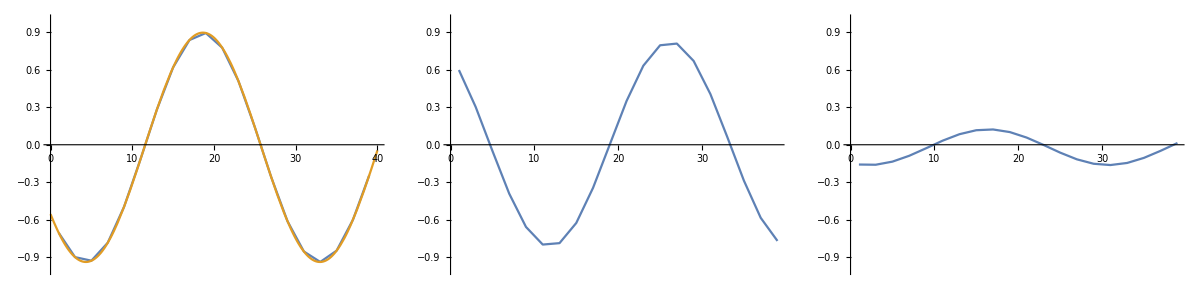

```mathematica
PhaseComp[n_]:=Module[{},pulseLT3=PurLT3.TotalPhaseCompGateLT3[n].rephasingLT3.KP[rzm,Subscript[σ, 0]].LDE2LT3.LDESwapLT3Y.InitLT3;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT3];
outState=measureOutAndBranch[outState,TomoLT3Z,TomoLT3Zmin];
outState=norm[outState];
Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]
phaseCompSweep=Table[{n,PhaseComp[n]},{n,1,40,2}];
Clear[x,a];
nlmLT3=NonlinearModelFit[phaseCompSweep,Amp*Cos[2π f x-a]+off,{{f,1/20},{a,2π},{Amp,1},{off,0.5}},x];
xx=Show[ListPlot[phaseCompSweep,Joined->{True}],Plot[Normal[nlmLT3],{x,0,40},PlotStyle->{ColorData[97,"ColorList"][[2]]}],PlotRange->{Automatic,{-1,1}}];
offsetLT3=Round[If[Amp>0,Mod[a,2π],Mod[a+π,2π]]/(2π f)/.nlmLT3["BestFitParameters"]]
If[Mod[offsetLT3,2]==0,offsetLT3=offsetLT3-1]

PhaseComp[n_]:=Module[{},pulseLT3=PurLT3.TotalPhaseCompGateLT3[n].rephasingLT3.KP[rzm,Subscript[σ, 0]].LDE2LT3.LDESwapLT3Y.InitLT3;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT3];
outState=measureOutAndBranch[outState,TomoLT3X,TomoLT3Xmin];
outState=norm[outState];
Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]
phaseCompSweep=Table[{n,PhaseComp[n]},{n,1,40,2}];
yy=ListPlot[phaseCompSweep,Joined->{True},PlotRange->{Automatic,{-1,1}}];

PhaseComp[n_]:=Module[{},pulseLT3=PurLT3.TotalPhaseCompGateLT3[n].rephasingLT3.KP[rzm,Subscript[σ, 0]].LDE2LT3.LDESwapLT3Y.InitLT3;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT3];
outState=measureOutAndBranch[outState,TomoLT3Y,TomoLT3Ymin];
outState=norm[outState];
Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]
phaseCompSweep=Table[{n,PhaseComp[n]},{n,1,40,2}];
zz=ListPlot[phaseCompSweep,Joined->{True},PlotRange->{Automatic,{-1,1}}];

Grid[{{xx,yy,zz}}]
```

#### Sequence

```mathematica
For[j=1,j≤3,j++,Print["Input " <>bases[[j]]];For[i=1,i≤3,i++,pulseLT3=KP[Subscript[𝒫, 0],Subscript[σ, 0]].PurLT3.TotalPhaseCompGateLT3[offsetLT3].rephasingLT3.LDE2LT3.initsLT3[[j]].InitLT3;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT3];
(*If[i==1,Print[PTr[{1},outState]//TableForm]];
*)outState=transformAndNorm[outState,tomosLT3[[i]]];

Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]]]]

Print["Min"]
For[j=1,j≤3,j++,Print["Input " <>bases[[j]]];For[i=1,i≤3,i++,pulseLT3=KP[Subscript[𝒫, 1],Subscript[σ, 0]].PurLT3.TotalPhaseCompGateLT3[offsetLT3].rephasingLT3.LDE2LT3.initsLT3[[j]].InitLT3;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=transformAndNorm[initState,pulseLT3];
(*If[i==1,Print[PTr[{1},outState]//TableForm]];
*)outState=transformAndNorm[outState,tomosLT3Min[[i]]];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].PTr[{2},outState]]]]]]]
```

Input X

X -0.287412

Y -0.48701

Z 0.978541

Input Y

X -0.00324057

Y -0.991661

Z 0.184867

Input Z

X 0.855292

Y -0.492184

Z -0.0592182

Min

Input X

X -0.170254

Y -0.717415

Z -0.710907

Input Y

X 0.00736967

Y 0.710801

Z -0.65899

Input Z

X 0.743407

Y -0.609092

Z -0.338186

## Purification

### Setup

```mathematica
PureLT4X=getPulses[basedirLT4,"AWG_seqs_Purify_XX"];
PureLT4Y=getPulses[basedirLT4,"AWG_seqs_Purify_YY"];
PureLT4Z=getPulses[basedirLT4,"AWG_seqs_Purify_ZZ"];
```

```mathematica
PureLT4X[[1;;9,1]]
PureLT4X[[86;;,1]]
PureLT4Y[[86;;,1]]
PureLT4Z[[86;;,1]]
```

(C_Init4_y_pt0_tau_0_N_0 | 1 | C_Init4_y_pt0_tau_0_N_0 | LDE10 | 0.000977248
LDE10 | 0 | None | LDE_rephasing_10 | 7.×10^-6
LDE1_final_0 | 0 | C_Init4_y_pt0_tau_0_N_0 | LDE_rephasing_10 | 7.×10^-6
LDE_rephasing_10 | 0 | C_Init4_y_pt0_tau_0_N_0 | LDE20 | 0.000978448
LDE20 | 0 | None | LDE_rephasing_2_0 | 7.×10^-6
LDE2_final_0 | 0 | C_Init4_y_pt0_tau_0_N_0 | LDE_rephasing_2_0 | 7.×10^-6
LDE_rephasing_2_0 | 0 | None | Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | 9.392×10^-6
Single_C13_Phase_correct0_0_DD_elt_tau_2298_N_2 | 0 | None | Single_Final_C13_correct_even0_DD_elt_tau_2298_N_2 | 9.192×10^-6
Single_C13_Phase_correct0_1_DD_elt_tau_2298_N_2 | 0 | None | Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | 9.192×10^-6)

(Single_Final_C13_correct_even0_DD_elt_tau_2298_N_2 | 0 | Purify_y_pi2_init0_tau_0_N_0 | None | 8.192×10^-6
Single_Final_C13_correct_odd0_DD_elt_tau_2298_N_2 | 0 | None | None | 0.000010192
Purify_y_pi2_init0_tau_0_N_0 | 0 | Tomo1_y_pi2_init0_tau_0_N_0 | Tomo0_y_pi2_init0_tau_0_N_0 | 0.0005358
Tomo0_y_pi2_init0_tau_0_N_0 | 0 | Rome_0 | None | 0.000454568
Tomo1_y_pi2_init0_tau_0_N_0 | 0 | None | None | 0.000454368)

```mathematica
For[z=1,z<=Dimensions[PureLT4X][[1]],z++,If[PureLT4X[[z,2]]!=PureLT4Y[[z,2]],Print[z]]]
For[z=1,z<=Dimensions[PureLT4X][[1]],z++,If[PureLT4X[[z,2]]!=PureLT4Z[[z,2]],Print[z]]]
Print["Elem length"]
For[z=1,z<=Dimensions[PureLT4X][[1]],z++,If[PureLT4X[[z,1,5]]!=PureLT4Z[[z,1,5]],Print[z]]]
For[z=1,z<=Dimensions[PureLT4X][[1]],z++,If[PureLT4X[[z,1,5]]!=PureLT4Z[[z,1,5]],Print[z]]]
```

89

90

89

90

Elem length

89

90

89

90

```mathematica
InitLT4=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,PureLT4X[[1]]];
LDELT4=compiledPulse[LT4C,PureLT4X[[2]]];
SwapLT4=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,PureLT4X[[4]]];
LDE2LT4=compiledPulse[LT4C,PureLT4X[[5]]];
rephasingLT4=compiledPulse[LT4C,PureLT4X[[7]]];
c13PhaseCorEvenLT4=compiledPulse[LT4C,PureLT4X[[8]]];
c13PhaseCorOddLT4=compiledPulse[LT4C,PureLT4X[[9]]];
c13FinalCorEvenLT4=compiledPulse[LT4C,PureLT4X[[86]]];
c13FinalCorOddLT4=compiledPulse[LT4C,PureLT4X[[87]]];
PurLT4=compiledPulse[LT4C,PureLT4X[[88]]];
TomoLT4X=compiledPulse[LT4C,PureLT4X[[89]]];
TomoLT4Y=compiledPulse[LT4C,PureLT4Y[[89]]];
TomoLT4Z=compiledPulse[LT4C,PureLT4Z[[89]]];
TomosLT4={TomoLT4X,TomoLT4Y,TomoLT4Z};
```

```mathematica
TotalPhaseCompGateLT4[n_]:=If[Mod[n,2]==0,c13FinalCorOddLT4.MatrixPower[c13PhaseCorOddLT4.c13PhaseCorEvenLT4,n/2],
c13FinalCorEvenLT4.c13PhaseCorEvenLT4.MatrixPower[c13PhaseCorOddLT4.c13PhaseCorEvenLT4,(n-1)/2]]
```

```mathematica
PureLT3X=getPulses[basedirLT3,"AWG_seqs_Pippin_SIL3_Purify_XX"];
PureLT3Y=getPulses[basedirLT3,"AWG_seqs_Pippin_SIL3_Purify_YY"];
PureLT3Z=getPulses[basedirLT3,"AWG_seqs_Pippin_SIL3_Purify_ZZ"];
```

```mathematica
PureLT3X[[1;;9,1]]
PureLT3X[[78;;,1]]
PureLT3Y[[78;;,1]]
PureLT3Z[[78;;,1]]
```

(C_Init1_y_pt0_tau_0_N_0 | 1 | C_Init1_y_pt0_tau_0_N_0 | LDE10 | 0.000977232
LDE10 | 0 | None | LDE_rephasing_10 | 7.×10^-6
LDE1_final_0 | 0 | C_Init1_y_pt0_tau_0_N_0 | LDE_rephasing_10 | 7.×10^-6
LDE_rephasing_10 | 0 | C_Init1_y_pt0_tau_0_N_0 | LDE20 | 0.000978432
LDE20 | 0 | None | LDE_rephasing_2_0 | 7.×10^-6
LDE2_final_0 | 0 | C_Init1_y_pt0_tau_0_N_0 | LDE_rephasing_2_0 | 7.×10^-6
LDE_rephasing_2_0 | 0 | None | Single_Final_C13_correct_odd0_DD_elt_tau_2310_N_2 | 9.46×10^-6
Single_C13_Phase_correct0_0_DD_elt_tau_2310_N_2 | 0 | None | Single_Final_C13_correct_even0_DD_elt_tau_2310_N_2 | 9.24×10^-6
Single_C13_Phase_correct0_1_DD_elt_tau_2310_N_2 | 0 | None | Single_Final_C13_correct_odd0_DD_elt_tau_2310_N_2 | 9.24×10^-6)

(Single_Final_C13_correct_even0_DD_elt_tau_2310_N_2 | 0 | Purify_y_pi2_init0_tau_0_N_0 | None | 8.24×10^-6
Single_Final_C13_correct_odd0_DD_elt_tau_2310_N_2 | 0 | None | None | 0.00001074
Purify_y_pi2_init0_tau_0_N_0 | 0 | Tomo1_y_pi2_init0_tau_0_N_0 | Tomo0_y_pi2_init0_tau_0_N_0 | 0.000361504
Tomo0_y_pi2_init0_tau_0_N_0 | 0 | Rome_0 | None | 0.00027984
Tomo1_y_pi2_init0_tau_0_N_0 | 0 | None | None | 0.000281068)

```mathematica
For[z=1,z<=Dimensions[PureLT3X][[1]],z++,If[PureLT3X[[z,2]]!=PureLT3Y[[z,2]],Print[z]]]
For[z=1,z<=Dimensions[PureLT3X][[1]],z++,If[PureLT3X[[z,2]]!=PureLT3Z[[z,2]],Print[z]]]
Print["Elem length"]
For[z=1,z<=Dimensions[PureLT3X][[1]],z++,If[PureLT3X[[z,1,5]]!=PureLT3Z[[z,1,5]],Print[z]]]
For[z=1,z<=Dimensions[PureLT3X][[1]],z++,If[PureLT3X[[z,1,5]]!=PureLT3Z[[z,1,5]],Print[z]]]
```

81

82

81

82

Elem length

81

82

81

82

```mathematica
InitLT3=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,PureLT3X[[1]]];
LDELT3=compiledPulse[LT3C,PureLT3X[[2]]];
SwapLT3=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,PureLT3X[[4]]];
LDE2LT3=compiledPulse[LT3C,PureLT3X[[5]]];
rephasingLT3=compiledPulse[LT3C,PureLT3X[[7]]];
c13PhaseCorEvenLT3=compiledPulse[LT3C,PureLT3X[[8]]];
c13PhaseCorOddLT3=compiledPulse[LT3C,PureLT3X[[9]]];
c13FinalCorEvenLT3=compiledPulse[LT3C,PureLT3X[[78]]];
c13FinalCorOddLT3=compiledPulse[LT3C,PureLT3X[[79]]];
PurLT3=compiledPulse[LT3C,PureLT3X[[80]]];
TomoLT3X=compiledPulse[LT3C,PureLT3X[[81]]];
TomoLT3Y=compiledPulse[LT3C,PureLT3Y[[81]]];
TomoLT3Z=compiledPulse[LT3C,PureLT3Z[[81]]];
TotalPhaseCompGateLT3[n_]:=KP[Subscript[σ, 0],rThetaZ[0.2]].If[Mod[n,2]==0,c13FinalCorOddLT3.MatrixPower[c13PhaseCorOddLT3.c13PhaseCorEvenLT3,n/2],
c13FinalCorEvenLT3.c13PhaseCorEvenLT3.MatrixPower[c13PhaseCorOddLT3.c13PhaseCorEvenLT3,(n-1)/2]]
TomosLT3={TomoLT3X,TomoLT3Y,TomoLT3Z};
```

### Non local!

Simulate this by tracing over the joint state after the LDE (this is fine since isnt entangled with the NV (to a reasonable approx)), adding in entangled state with pi X pulse (to end up in right state)

#### Same detectors click

```mathematica
θ=π/4;
rawState = Sin[θ]^2*ρfromψ[KP[Ket[0],Ket[0]]]+Cos[θ]^2*ρfromψ[1/(√2)*(KP[Ket[0],Ket[1]]+KP[Ket[1],Ket[0]])];
rawState2 =Sin[θ]^2*ρfromψ[KP[Ket[0],Ket[0]]]+Cos[θ]^2*ρfromψ[1/(√2)*(KP[Ket[0],Ket[1]]+KP[Ket[1],Ket[0]])];

rawStateXrot=KP[rXp,rXp].rawState.KP[rXp,rXp];
rawState2Xrot=KP[rXp,rXp].rawState2.KP[rXp,rXp];
```

```mathematica
initPulse=KP[LDELT3.InitLT3,LDELT4.InitLT4];
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2,Subscript[𝒫, 0],Subscript[σ, 0]/2];
initCState=PTr[{1,3},transformAndNorm[initState,initPulse]];
```

```mathematica
firstClickState=Raffleρ4Q[KP[rawStateXrot,initCState]];
swapPulse=KP[LDE2LT3.SwapLT3,LDE2LT4.SwapLT4];
swapCState=PTr[{1,3},transformAndNorm[firstClickState,swapPulse]];
```

```mathematica
secondClickState=Raffleρ4Q[KP[rawState2Xrot,swapCState]];
purPulse=KP[KP[Subscript[𝒫, 0],Subscript[σ, 0]].PurLT3.TotalPhaseCompGateLT3[offsetLT3].rephasingLT3, KP[Subscript[𝒫, 0],Subscript[σ, 0]].PurLT4.TotalPhaseCompGateLT4[offsetLT4].rephasingLT4];
purState=transformAndNorm[secondClickState,purPulse];
```

```mathematica
Print["Carbons state before tomo"]
Print[PTr[{1,3},purState]//Chop//TableForm];
For[x=1,x≤3,x++,
tomoPulse=KP[TomosLT3[[x]],TomosLT4[[x]]];
outState=PTr[{2,4},transformAndNorm[purState,tomoPulse]];
Print[bases[[x]]];
Print["Corr "<> ToString@Re[Tr[KP[Subscript[σ, 3],Subscript[σ, 3]].outState]]];
Print[Re[Tr[KP[Subscript[𝒫, 0],Subscript[𝒫, 0]].outState]]];
Print[Re[Tr[KP[Subscript[𝒫, 0],Subscript[𝒫, 1]].outState]]];
Print[Re[Tr[KP[Subscript[𝒫, 1],Subscript[𝒫, 0]].outState]]];
Print[Re[Tr[KP[Subscript[𝒫, 1],Subscript[𝒫, 1]].outState]]];]
```

Carbons state before tomo

0.447163 | 0.0292762-0.0253809 ⅈ | 0.0237997-0.0280454 ⅈ | 0.110642+0.308851 ⅈ
0.0292762+0.0253809 ⅈ | 0.0679675 | -0.0187477-0.0518094 ⅈ | -0.0490396-0.0751587 ⅈ
0.0237997+0.0280454 ⅈ | -0.0187477+0.0518094 ⅈ | 0.0549083 | 0.0850151+0.0278822 ⅈ
0.110642-0.308851 ⅈ | -0.0490396+0.0751587 ⅈ | 0.0850151-0.0278822 ⅈ | 0.429961

X

Corr -0.556265

0.000374648

0.392455

0.385677

0.221493

Y

Corr 0.773271

0.448836

0.053418

0.0599463

0.437799

Z

Corr 0.709122

0.435211

0.0878533

0.0575857

0.41935

#### Different detectors

```mathematica
θ=π/4;
rawState = Sin[θ]^2*ρfromψ[KP[Ket[0],Ket[0]]]+Cos[θ]^2*ρfromψ[1/(√2)*(KP[Ket[0],Ket[1]]+KP[Ket[1],Ket[0]])];
rawState2 =Sin[θ]^2*ρfromψ[KP[Ket[0],Ket[0]]]+Cos[θ]^2*ρfromψ[1/(√2)*(KP[Ket[0],Ket[1]]-KP[Ket[1],Ket[0]])];

rawStateXrot=KP[rXp,rXp].rawState.KP[rXp,rXp];
rawState2Xrot=KP[rXp,rXp].rawState2.KP[rXp,rXp];
```

```mathematica
initPulse=KP[LDELT3.InitLT3,LDELT4.InitLT4];
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2,Subscript[𝒫, 0],Subscript[σ, 0]/2];
initCState=PTr[{1,3},transformAndNorm[initState,initPulse]];
```

```mathematica
firstClickState=Raffleρ4Q[KP[rawStateXrot,initCState]];
swapPulse=KP[LDE2LT3.SwapLT3,LDE2LT4.SwapLT4];
swapCState=PTr[{1,3},transformAndNorm[firstClickState,swapPulse]];
```

```mathematica
secondClickState=Raffleρ4Q[KP[rawState2Xrot,swapCState]];
purPulse=KP[KP[Subscript[𝒫, 0],Subscript[σ, 0]].PurLT3.TotalPhaseCompGateLT3[offsetLT3].rephasingLT3, KP[Subscript[𝒫, 0],Subscript[σ, 0]].PurLT4.TotalPhaseCompGateLT4[offsetLT4].rephasingLT4];
purState=transformAndNorm[secondClickState,purPulse];
```

```mathematica
Print["Carbons state before tomo"]
Print[PTr[{1,3},purState]//Chop//TableForm];
For[x=1,x≤3,x++,
tomoPulse=KP[TomosLT3[[x]],TomosLT4[[x]]];
outState=PTr[{2,4},transformAndNorm[purState,tomoPulse]];
Print[bases[[x]]];
Print["Corr "<> ToString@Re[Tr[KP[Subscript[σ, 3],Subscript[σ, 3]].outState]]];
Print[Re[Tr[KP[Subscript[𝒫, 0],Subscript[𝒫, 0]].outState]]];
Print[Re[Tr[KP[Subscript[𝒫, 0],Subscript[𝒫, 1]].outState]]];
Print[Re[Tr[KP[Subscript[𝒫, 1],Subscript[𝒫, 0]].outState]]];
Print[Re[Tr[KP[Subscript[𝒫, 1],Subscript[𝒫, 1]].outState]]];]
```

Carbons state before tomo

0.0692284 | 0.0412782+0.0287498 ⅈ | -0.0485353-0.0681707 ⅈ | -0.0178163-0.0501942 ⅈ
0.0412782-0.0287498 ⅈ | 0.444385 | 0.0822611+0.319162 ⅈ | 0.0202574-0.0345318 ⅈ
-0.0485353+0.0681707 ⅈ | 0.0822611-0.319162 ⅈ | 0.43489 | 0.0729625-0.0293271 ⅈ
-0.0178163+0.0501942 ⅈ | 0.0202574+0.0345318 ⅈ | 0.0729625+0.0293271 ⅈ | 0.0514969

X

Corr -0.556614

0.000129289

0.39255

0.385757

0.221564

Y

Corr -0.77325

0.0592516

0.440213

0.446412

0.0541236

Z

Corr -0.693075

0.0851112

0.436985

0.409553

0.068351